```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/oernst/Research/cnl/dynamic_boltzmann_cpp/helix

Params

```mathematica
dir="data_learned/";
```

### N opt steps

```mathematica
nOpt=800;
```

### Time

```mathematica
tGrid=Flatten[Import[dir<>"grid_time.txt","Table"]];
nt=Length[tGrid];
tmax=tGrid[[-1]];
```

### Space

```mathematica
{nuMinMax["hA"],nuMinMax["hB"]}=Transpose[Import[dir<>"grid_F_hA.txt","Table"]][[;;,{1,-1}]];
```

### Moments

```mathematica
momsMinMax=Association[];
momsMinMax["hA"]={0,300};
momsMinMax["hB"]={0,300};
momsMinMax["hC"]={0,300};
```

Moments

```mathematica
pts={};
Do[
latt=Import["stoch_sim/lattice_v001/lattice/"<>IntegerString[i,10,4]<>".txt","Table"];
nA=Length[Select[latt,#[[2]]=="A"&]];
nB=Length[Select[latt,#[[2]]=="B"&]];
nC=Length[Select[latt,#[[2]]=="C"&]];
AppendTo[pts,{nA,nB,nC}];
,{i,0,100}]
```

```mathematica
ListPointPlot3D[pts]/.Point->Line
```

-Graphics3D-

```mathematica
pts={};
Do[
latt=Import["stoch_sim/lattice_v001/lattice/"<>IntegerString[i,10,4]<>".txt","Table"];
nA=Length[Select[latt,#[[2]]=="A"&]];
nB=Length[Select[latt,#[[2]]=="B"&]];
AppendTo[pts,{nA,nB}];
,{i,0,100}]
```

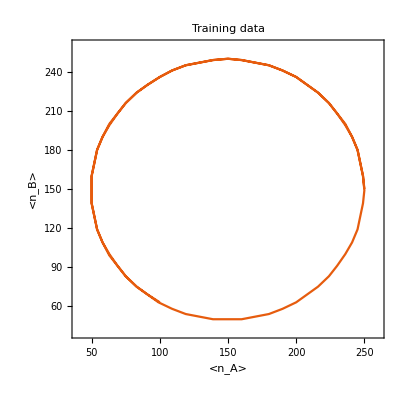

```mathematica
plt=ListLinePlot[pts,AspectRatio->1,PlotRange->{{40,260},{40,260}},FrameLabel->{"<n_A>","<n_B>"},PlotLabel->"Training data"]
```

```mathematica
Export["/Users/oernst/Research/cnl/multiscale/*doi_boltzmann_eric_dkl/hidden_layers/figures/circular.pdf",plt];
```

Moments dynamic

```mathematica
Manipulate[
Quiet[Check[
fmhA=Import[dir<>"/moments/hA_"<>IntegerString[iOpt,10,4]<>".txt","Table"];
fmhB=Import[dir<>"/moments/hB_"<>IntegerString[iOpt,10,4]<>".txt","Table"];
fmhC=Import[dir<>"/moments/hC_"<>IntegerString[iOpt,10,4]<>".txt","Table"];
GraphicsGrid[{
{ListLinePlot[Transpose[fmhA],PlotRange->{{0,nt-1},momsMinMax["hA"]}],ListLinePlot[Transpose[fmhB],PlotRange->{{0,nt-1},momsMinMax["hB"]}],ListLinePlot[Transpose[fmhC],PlotRange->{{0,nt-1},momsMinMax["hC"]}]}
},ImageSize->1000]
,
(* Fail *)
"Fail"
]]
,{iOpt,0,nOpt-1,1}]
```

### Example figure

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

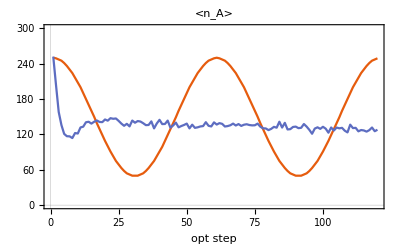
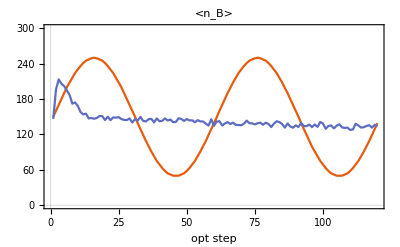
-Graphics- | -Graphics- |

```mathematica
iOptFig=555;
fmhA=Import[dir<>"/moments/hA_"<>IntegerString[iOptFig,10,4]<>".txt","Table"];
fmhB=Import[dir<>"/moments/hB_"<>IntegerString[iOptFig,10,4]<>".txt","Table"];
plt2=Grid[{{
ListLinePlot[Transpose[fmhA],PlotRange->{{0,120},momsMinMax["hA"]},FrameLabel->{"opt step"},PlotLabel->"<n_A>"],
ListLinePlot[Transpose[fmhB],PlotRange->{{0,120},momsMinMax["hB"]},FrameLabel->{"opt step"},PlotLabel->"<n_B>"],
LineLegend[{colors[[1]],colors[[2]]},{"Training data","CD=10"},LabelStyle->{FontSize->24}]
}}]
```

```mathematica
Export["/Users/oernst/Research/cnl/multiscale/*doi_boltzmann_eric_dkl/hidden_layers/figures/circular_moments_fail.pdf",plt2];
```

Nu

```mathematica
Manipulate[
Quiet[Check[
fnuhA=Flatten[Import[dir<>"/ixn_params/hA_"<>IntegerString[iOpt,10,4]<>".txt","Table"]];
fnuhB=Flatten[Import[dir<>"/ixn_params/hB_"<>IntegerString[iOpt,10,4]<>".txt","Table"]];
fnuhC=Flatten[Import[dir<>"/ixn_params/hC_"<>IntegerString[iOpt,10,4]<>".txt","Table"]];
GraphicsGrid[{
{ListLinePlot[fnuhA,PlotRange->{{0,nt-1},nuMinMax["hA"]}],ListLinePlot[fnuhB,PlotRange->{{0,nt-1},nuMinMax["hB"]}],ListLinePlot[fnuhC,PlotRange->{{0,nt-1},nuMinMax["hC"]}]}
},ImageSize->1000]
,
(* Fail *)
"Fail"
]]
,{iOpt,0,nOpt-1,1}]
```

```mathematica
ListPointPlot3D[Transpose[{fnuhA,fnuhB,fnuhC}]]/.Point->Line
```

-Graphics3D-

Variational terms

```mathematica
varhAfA=Import[dir<>"/var_terms/var_hA_wrt_F_hA_0020.txt","Table"]
```

{1}
 |  |  |  |

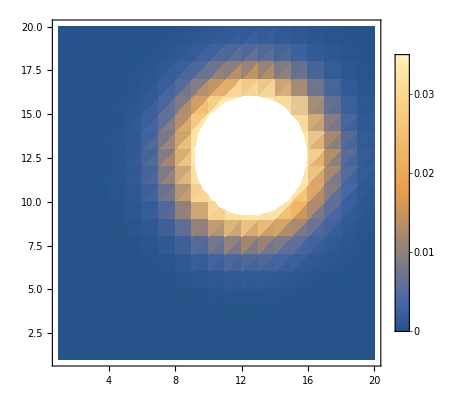

```mathematica
var=ArrayReshape[varhAfA[[;;,30]],{20,20}];
ListDensityPlot[var,PlotLegends->Automatic]
```

```mathematica
Dimensions[varhAfA]
```

{400,200}